## Cellular Potts Model

### f(x)

```mathematica
(* cross and moore neighbour indices within bounds of the canvas *)
crossneighbours[{p_,q_}]:=DeleteCases[{
{p,q-1},
{p,q+1},
{p-1,q},
{p+1,q}},{OrderlessPatternSequence[x_/;x≤0||x>n,_]},{1}];

mooreneighbours[{p_,q_}]:=DeleteCases[{
{p,q-1},
{p,q+1},
{p-1,q-1},
{p-1,q},
{p-1,q+1},
{p+1,q-1},
{p+1,q},
{p+1,q+1}},{OrderlessPatternSequence[x_/;x≤0||x>n,_]},{1}];
```

```mathematica
(* boundary points of all cells together *)
boundarymerger[assoc_]:=DeleteDuplicates[Cases[Normal@assoc,{__Integer}..,{-2}]]
```

```mathematica
(* local adhesive energy *)
Clear@localAdhesionEnergyCalc;
localAdhesionEnergyCalc[{x_,y_}]:=Block[{neigh=crossneighbours[{x,y}],elem,C=({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}}),kronec=({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}}),cellid},
elem=Extract[A,neigh];
(* counts *)
With[{ind=A[[x,y]]},
Do[
If[j==ind,
C[[j+1,ind+1]]+=1,
C[[ind+1,j+1]]+=1
]
,{j,elem}]
];

(* same cell or dissimilar matrix *)
With[{cell=pixToCellAssoc[{x,y}]},
Do[
cellid=A[[j]];
If[cellid==cell,
(*neighbour belongs to the same cell*)
kronec[[cellid+1,cell+1]]+=1-KroneckerDelta[cell,cellid],
(*neighbour from a different cell*)
kronec[[cell+1,cellid+1]]+=1-KroneckerDelta[cell,cellid]
]
,{j,neigh}]
];
Total[({{1, 1, 1}, {1, 0.5, 0.5}, {1, 0.5, 0.5}})kronec C J,2]
];
```

```mathematica
(* total adhesive energy for all cells *)
Clear@globalAdhesionEnergy;
globalAdhesionEnergy[assoc_]:=Total[localAdhesionEnergyCalc/@boundarymerger[assoc]]
```

```mathematica
(* energy because of cell area and perimeter away from rest params *)
Clear@springEnergy;
springEnergy[{celltype_,{_,area_,peri_}}]:=Block[{k=Kparam[celltype]},
k[ka]((area - a0)^2)+k[kp]((peri - p0)^2)
];
```

```mathematica
(* total energy of the system *)
Clear@globalTotalEnergy;
globalTotalEnergy[assoc_]:=Total[Map[springEnergy,assoc]]+globalAdhesionEnergy[assoc]
```

```mathematica
Clear@fun;Clear@xx;
fun=Function[x,
Which[Length[xx=Union@Extract[A,mooreneighbours@x]]>1,x,
Length[xx]==1&&(Complement[xx,A[[x]]])≠{},x,
True,Nothing]
];
```

### params

```mathematica
n=100; (* canvas size *)
```

```mathematica
(* adhesion strength *)
Subscript[j, 00]= 0;Subscript[j, 11]=6;Subscript[j, 22]=6;
Subscript[j, 01]=Subscript[j, 10]=6;
Subscript[j, 02]=Subscript[j, 20]=6;
Subscript[j, 12]=Subscript[j, 21]=16;

J=({{Subscript[j, 00], Subscript[j, 01], Subscript[j, 02]}, {Subscript[j, 10], Subscript[j, 11], Subscript[j, 12]}, {Subscript[j, 20], Subscript[j, 21], Subscript[j, 22]}});
```

```mathematica
a0=100;p0=1; (* rest parameters *)
Kparam=<|1-><|ka-> 1,kp->2|>,2-><|ka-> 1,kp->2|>|>; (*stifness params*)
T=20;(*temperatures*)
```

```mathematica
iter=1000; (* number of iterations *)
```

```mathematica
A=ConstantArray[0,{n,n}]; (* empty canvas *)
```

### CPM lattice

```mathematica
shift={30,30};
pos=shift+#&/@Position[DiskMatrix[20],1];
Scan[(A[[Sequence@@#]]=1)&,pos]
```

```mathematica
(*
Table[shift={35+i,40+j};
pos=shift+#&/@Position[DiskMatrix[2],1];
Scan[(A[[Sequence@@#]]=2)&,pos],{i,Range[1,28,8]},{j,Range[1,20,8]}];
*)
```

```mathematica
saltpepper=Array[RandomChoice[{1,2}]&,{n,n}];
```

```mathematica
A=A*saltpepper;
```

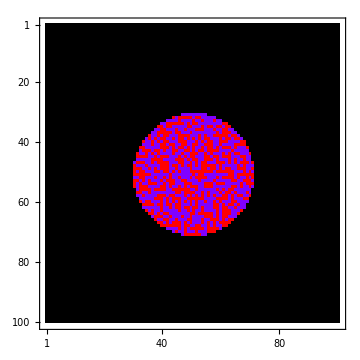

```mathematica
pltinitial=plt=MatrixPlot[A,ColorFunction->Hue,ColorRules->{0->Black},ImageSize->Medium]
```

### initial properties

```mathematica
components=MapAt[
Values@ComponentMeasurements[MorphologicalComponents[#,CornerNeighbors->False],{"Mask","Area","PerimeterLength"}]&,
ComponentMeasurements[A,"Mask"],{All,2}];
assoc=<|MapIndexed[First[#2]-> {#[[1]],#1[[2]]}&,Flatten@Map[Thread,components]]|>;
assocT=MapAt[Map[fun]@*(Position[ImageData@MorphologicalPerimeter@Image[#],1]&),assoc,{All,2,1}];
pixToCellAssoc=AssociationMap[Thread[#[[2,2,1]]-> First[#]]&,assocT];
pixToTypeAssoc=AssociationMap[Thread[#[[2,2,1]]-> #[[2,1]]]&,assocT];
totalE=globalTotalEnergy[assocT];
```

### simulate CPM

```mathematica
ls=CreateDataStructure["DynamicArray"]
```

DataStructure[DynamicArray, {Data -> {}}]

```mathematica
Off[General::munfl];
Block[{t,prevEnergy=totalE,randpt,prevtype,opts,newcelltype,components,newtotalE,T=T,componentsprev=components,assocprev=assoc,assocTprev=assocT,assoc=assoc,assocT=assocT,p,newlatticesite,neighbours,cellnum,pixToCellAssoc=pixToCellAssoc,pixToTypeAssoc=pixToTypeAssoc},
t=0;
Monitor[
While[t<iter,
(* pick a random boundary pt and get its 4-neighbours for mutation *)
p=assocT[RandomChoice@*Range@*Length@assocT][[2,1]];
If[p≠ {},
randpt=RandomChoice[p]; (*random boundary pt*)
prevtype=A[[Sequence@@randpt]];
cellnum=pixToCellAssoc[randpt];
neighbours=crossneighbours[randpt];
opts=Position[Lookup[pixToCellAssoc,neighbours]/._Missing->0,Except[cellnum],{1},Heads->False];
(*Pick[neighbours,KroneckerDelta@@@Thread[{pixToCellAssoc[randpt],Lookup[pixToCellAssoc,neighbours]/. _Missing->0}],0];*)
If[opts≠ {},
newlatticesite=RandomChoice@Extract[neighbours,opts];
newcelltype=Extract[A,newlatticesite];
A[[Sequence@@randpt]]=newcelltype;

(* compute local energy change *)
components=MapAt[
Values@ComponentMeasurements[MorphologicalComponents[#,CornerNeighbors->False],{"Mask","Area","PerimeterLength"}]&,
ComponentMeasurements[A,"Mask"],{All,2}];
assoc=<|MapIndexed[First[#2]-> {#[[1]],#1[[2]]}&,Flatten@Map[Thread,components]]|>;
assocT=MapAt[Map[fun]@*(Position[ImageData@MorphologicalPerimeter@Image[#],1]&),assoc,{All,2,1}];
newtotalE= globalTotalEnergy[assocT];
pixToCellAssoc=AssociationMap[Thread[#[[2,2,1]]-> First[#]]&,assocT];(*pixToTypeAssoc=AssociationMap[Thread[#[[2,2,1]]-> #[[2,1]]]&,assocT];*)
(* acceptance, rejection step *)
If[newtotalE< prevEnergy,
(*accept it*)
ls["Append",newtotalE];
prevEnergy=newtotalE,
If[RandomReal[1]<Exp[-(newtotalE-prevEnergy)/T],
(*accept it by probability*)
ls["Append",newtotalE];
prevEnergy=newtotalE,
(*return to the previous state*)
A[[Sequence@@randpt]]=prevtype;
components=componentsprev;
assoc=assocprev;
assocT=assocTprev;
pixToCellAssoc=AssociationMap[Thread[#[[2,2,1]]-> First[#]]&,assocT];(*pixToTypeAssoc=AssociationMap[Thread[#[[2,2,1]]-> #[[2,1]]]&,assocT];*)
ls["Append",prevEnergy];
]
];
];
componentsprev=components;
assocprev=assoc;
assocTprev=assocT;
plt=MatrixPlot[A,ColorFunction->Hue,ColorRules->{0->Black},ImageSize->Medium];
(*Export["C:\\Users\\aliha\\Desktop\\save\\"<>ToString[t]<>".jpg",plt];*)
t+=1
]
],{t,plt}]
];
On[General::munfl];
```

### results

```mathematica
ls["Length"]
```

14670

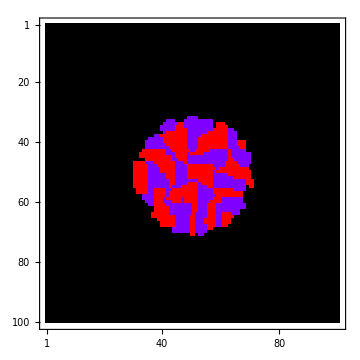
-Graphics--Graphics-

```mathematica
Row[{pltinitial,plt}]
```

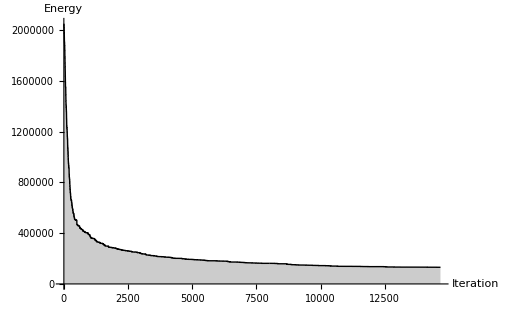

```mathematica
ListLinePlot[Normal@ls,PlotStyle->{Thick,Black},Filling->Axis,
AxesStyle->Directive[Black,Bold, 12],AxesLabel->{"Iteration","Energy"},ImageSize->512,PlotRange->All]
```